```mathematica
<<sneg`;
```

sneg 1.226 Copyright (C) 2010 Rok Zitko

```mathematica
S=1
sx=spinmatrixX[S]
sy=spinmatrixY[S]
sz=spinmatrixZ[S]
```

1

{{0,1/(√2),0},{1/(√2),0,1/(√2)},{0,1/(√2),0}}

{{0,-ⅈ/(√2),0},{ⅈ/(√2),0,-ⅈ/(√2)},{0,ⅈ/(√2),0}}

{{1,0,0},{0,0,0},{0,0,-1}}

1

{{1+B,0,0},{0,0,0},{0,0,1-B}}

{{0,1-B,1+B},{{0,1,0},{0,0,1},{1,0,0}}}

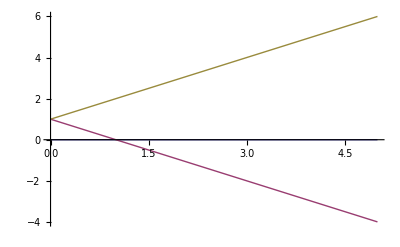

```mathematica
d=1
H=B sz+d sz.sz
{val,vec}=Eigensystem[H]
Plot[val,{B,0,5}]
```

1

{{1,B/(√2),0},{B/(√2),0,B/(√2)},{0,B/(√2),1}}

{{1,1/2 (1-√(1+4 B^2)),1/2 (1+√(1+4 B^2))},{{-1,0,1},{1,-(1+√(1+4 B^2))/(√2 B),1},{1,(-1+√(1+4 B^2))/(√2 B),1}}}

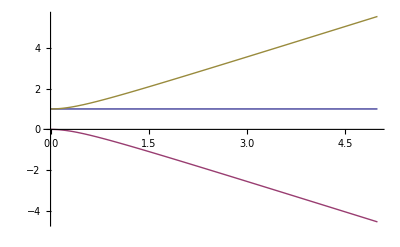

```mathematica
d=1
H=B sx+d sz.sz
{val,vec}=Eigensystem[H]
Plot[val,{B,0,5}]
```

```mathematica
S=5/2
sx=spinmatrixX[S]
sy=spinmatrixY[S]
sz=spinmatrixZ[S]
```

5/2

{{0,(√5)/2,0,0,0,0},{(√5)/2,0,√2,0,0,0},{0,√2,0,3/2,0,0},{0,0,3/2,0,√2,0},{0,0,0,√2,0,(√5)/2},{0,0,0,0,(√5)/2,0}}

{{0,-(ⅈ √5)/2,0,0,0,0},{(ⅈ √5)/2,0,-ⅈ √2,0,0,0},{0,ⅈ √2,0,-(3 ⅈ)/2,0,0},{0,0,(3 ⅈ)/2,0,-ⅈ √2,0},{0,0,0,ⅈ √2,0,-(ⅈ √5)/2},{0,0,0,0,(ⅈ √5)/2,0}}

{{5/2,0,0,0,0,0},{0,3/2,0,0,0,0},{0,0,1/2,0,0,0},{0,0,0,-1/2,0,0},{0,0,0,0,-3/2,0},{0,0,0,0,0,-5/2}}

1

0.2

{{25/4,(√5 B)/2,0.632456,0,0,0},{(√5 B)/2,9/4,√2 B,0.848528,0,0},{0.632456,√2 B,1/4,(3 B)/2,0.848528,0},{0,0.848528,(3 B)/2,1/4,√2 B,0.632456},{0,0,0.848528,√2 B,9/4,(√5 B)/2},{0,0,0,0.632456,(√5 B)/2,25/4}}

Eigensystem::eivec0: Unable to find all eigenvectors.

{{Root[3.55087-12.4492 B^2+144.262 B^4-3.51563 B^6+(56.7856+464.567 B^2-109.094 B^4) #1+(194.053-416.161 B^2+16.1875 B^4) #1^2+(-259.913+109.55 B^2) #1^3+(106.697-8.75 B^2) #1^4-17.5 #1^5+#1^6&,1],Root[3.55087-12.4492 B^2+144.262 B^4-3.51563 B^6+(56.7856+464.567 B^2-109.094 B^4) #1+(194.053-416.161 B^2+16.1875 B^4) #1^2+(-259.913+109.55 B^2) #1^3+(106.697-8.75 B^2) #1^4-17.5 #1^5+#1^6&,2],Root[3.55087-12.4492 B^2+144.262 B^4-3.51563 B^6+(56.7856+464.567 B^2-109.094 B^4) #1+(194.053-416.161 B^2+16.1875 B^4) #1^2+(-259.913+109.55 B^2) #1^3+(106.697-8.75 B^2) #1^4-17.5 #1^5+#1^6&,3],Root[3.55087-12.4492 B^2+144.262 B^4-3.51563 B^6+(56.7856+464.567 B^2-109.094 B^4) #1+(194.053-416.161 B^2+16.1875 B^4) #1^2+(-259.913+109.55 B^2) #1^3+(106.697-8.75 B^2) #1^4-17.5 #1^5+#1^6&,4],Root[3.55087-12.4492 B^2+144.262 B^4-3.51563 B^6+(56.7856+464.567 B^2-109.094 B^4) #1+(194.053-416.161 B^2+16.1875 B^4) #1^2+(-259.913+109.55 B^2) #1^3+(106.697-8.75 B^2) #1^4-17.5 #1^5+#1^6&,5],Root[3.55087-12.4492 B^2+144.262 B^4-3.51563 B^6+(56.7856+464.567 B^2-109.094 B^4) #1+(194.053-416.161 B^2+16.1875 B^4) #1^2+(-259.913+109.55 B^2) #1^3+(106.697-8.75 B^2) #1^4-17.5 #1^5+#1^6&,6]},{{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0}}}

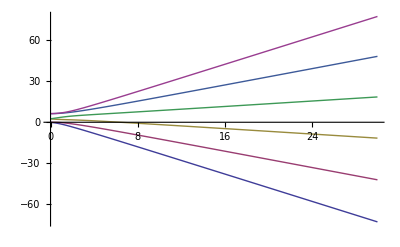

```mathematica
d=1
e=0.2
H=B sx+d sz.sz+e(sx.sx-sy.sy)
{val,vec}=Eigensystem[H]
Plot[val,{B,0,30}]
```